#### Global Variables

```mathematica
prec=100;

Nmax = 100;

x = 20.0;

xmax = 20.0;
xmin = -20.0;
xsize = 100;
dx=(xmax-xmin)/(xsize-1);

Xvector = N[Range[xmin,xmax,dx],prec];
Nvector = Range[0,Nmax,1];
```

#### Wavefuntion_Wolfram_Mathematica_1

```mathematica
WavefunctionMathematica1[n_,x_,prec_]:=Module[{nPrec,xPrec,norm,H,wavefunction},
SetPrecision[n,prec];
SetPrecision[x,prec];
norm=(2^(-0.5*n))*(Gamma[n+1]^(-0.5))*(Pi^(-0.25));
H=HermiteH[n,x];
wavefunction=SetPrecision[norm*Exp[-0.5*x^2]*H,prec];
wavefunction];
```

#### Wavefuntion_Wolfram_Mathematica_2

```mathematica
WavefunctionMathematica2[n_,x_,prec_]:=Module[{wavefunction,xsize,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
wavefunction[[2]]=SetPrecision[(2 x wavefunction[[1]])/Sqrt[2],prec];
For[i=3,i<=n+1,i++,wavefunction[[i]]=2 x (wavefunction[[i-1]]/Sqrt[2 (i-1)])-Sqrt[(i-2)/(i-1)] wavefunction[[i-2]];];
wavefunction[[n+1]]];
```

#### Wavefuntion_Wolfram_Mathematica_3

```mathematica
WavefunctionMathematica3[n_,x_,prec_]:=Module[{wavefunction,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
For[i=1,i<=n,i++,
wavefunction[[i+1]]=
SetPrecision[2 x (wavefunction[[i]]/Sqrt[2 (i)])-
Sqrt[(i-1)/i] wavefunction[[i-1]],prec]];

wavefunction];
```

#### Tests

Single Fock and Single Position speed test with the Normalized Coefficients Matrix

Functionality Test Passed: True

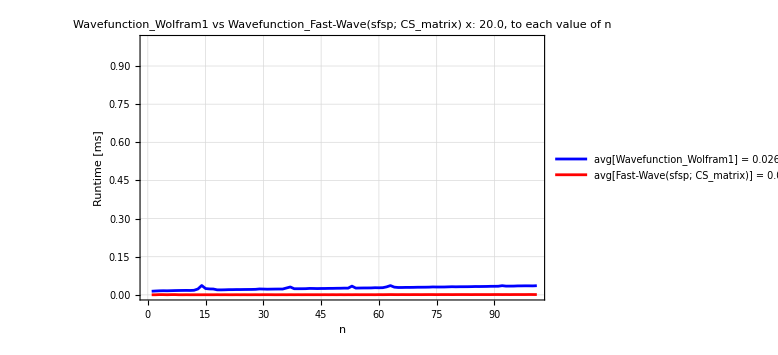

```mathematica
(*To use timeit.repeat in the Python is a option too*)

FastWaveSFSPList=Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_numba as wn;import timeit;N_max = 100;x = 20.0;[(timeit.timeit(lambda : wn.psi_n_single_fock_single_position(n, x) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSFSPList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSFSPList,
RepeatedTiming[WavefunctionMathematica1[i-1,x,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSFSPList,FastWaveSFSPList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(sfsp; CS_matrix)",Bold,13],"\n",Style["x: 20.0, to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSFSPList],20],TraditionalForm] <> " ms;" ,
" avg[Fast-Wave(sfsp; CS_matrix)] = "<> ToString[SetPrecision[Mean[FastWaveSFSPList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.0}}
]
```

#### Single Fock and Single Position speed test

Functionality Test Passed: True

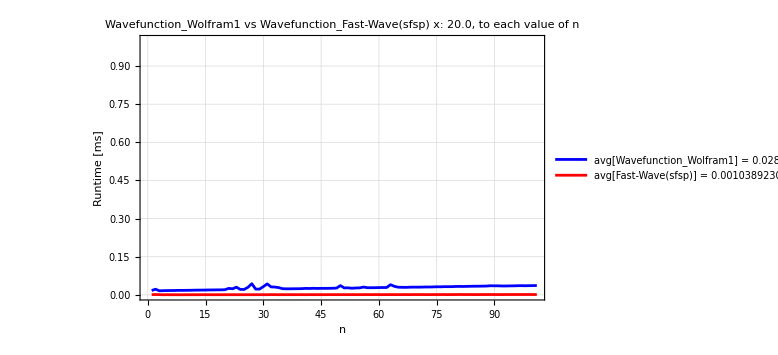

```mathematica
FastWaveSFSPList=Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_numba as wn;import timeit;N_max = 100;x = 20.0;[(timeit.timeit(lambda : wn.psi_n_single_fock_single_position(n, x, CS_matrix=False) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSFSPList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSFSPList,
RepeatedTiming[WavefunctionMathematica1[i-1,x,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSFSPList,FastWaveSFSPList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(sfsp)",Bold,13],"\n",Style["x: 20.0, to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSFSPList],20],TraditionalForm] <> " ms;" ,
" avg[Fast-Wave(sfsp)] = "<> ToString[SetPrecision[Mean[FastWaveSFSPList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.0}}
]
```

#### Single Fock and Multiple Position speed test with the Normalized Coefficients Matrix

Functionality Test Passed: True

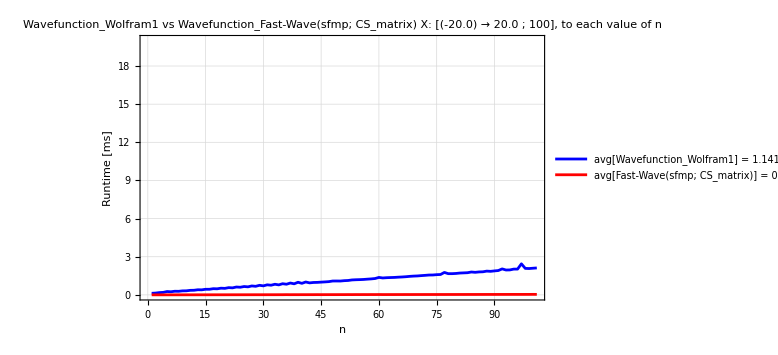

```mathematica
FastWaveSFMPList=Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_numba as wn;import timeit;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[(timeit.timeit(lambda : wn.psi_n_single_fock_multiple_position(n, X) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSFMPList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSFMPList,
RepeatedTiming[WavefunctionMathematica1[i-1,Xvector,prec]][[1]]*1000];]
ListLinePlot[
{WavefunctionWolframSFMPList,FastWaveSFMPList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(sfmp; CS_matrix)",Bold,13],"\n",Style["X: [(-20.0) → 20.0 ; 100], to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSFMPList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(sfmp; CS_matrix)] = "<> ToString[SetPrecision[Mean[FastWaveSFMPList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ,PlotRange->{{Automatic,Automatic},{0,20.0}}
]
```

#### Single Fock and Multiple Position speed test

Functionality Test Passed: True

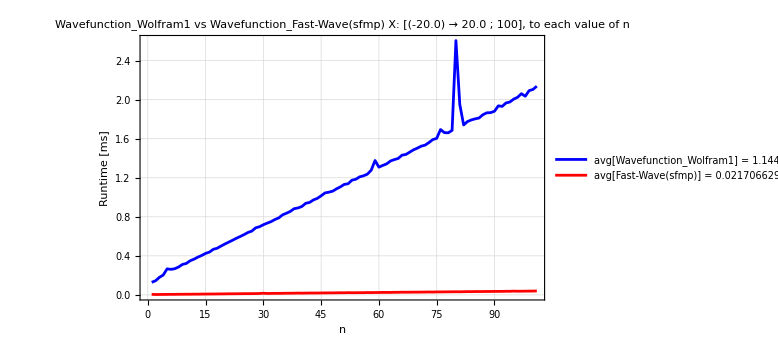

```mathematica
FastWaveSFMPList=Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_numba as wn;import timeit;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[(timeit.timeit(lambda : wn.psi_n_single_fock_multiple_position(n, X, CS_matrix = False) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSFMPList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSFMPList,
RepeatedTiming[WavefunctionMathematica1[i-1,Xvector,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSFMPList,FastWaveSFMPList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(sfmp)",Bold,13],"\n",Style["X: [(-20.0) → 20.0 ; 100], to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSFMPList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(sfmp)] = "<> ToString[SetPrecision[Mean[FastWaveSFMPList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```

#### Multiple Fock and Single Position speed test

Functionality Test Passed: True

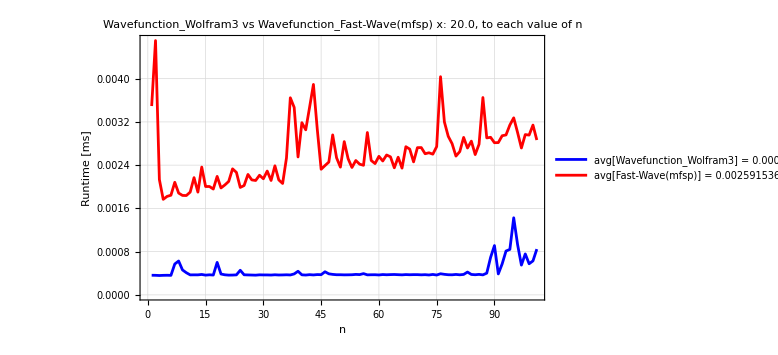

```mathematica
FastWaveMFSPList=Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_numba as wn;import timeit;N_max = 100;x = 20.0;[(timeit.timeit(lambda : wn.psi_n_multiple_fock_single_position(n, x) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframMFSPList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframMFSPList,
RepeatedTiming[WavefunctionMathematica3[i-1,x,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframMFSPList,FastWaveMFSPList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mfsp)",Bold,13],"\n",Style["x: 20.0, to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram3] = " <>ToString[SetPrecision[Mean[WavefunctionWolframMFSPList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(mfsp)] = "<> ToString[SetPrecision[Mean[FastWaveMFSPList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```

#### Multiple Fock and Multiple Position speed test

Functionality Test Passed: True

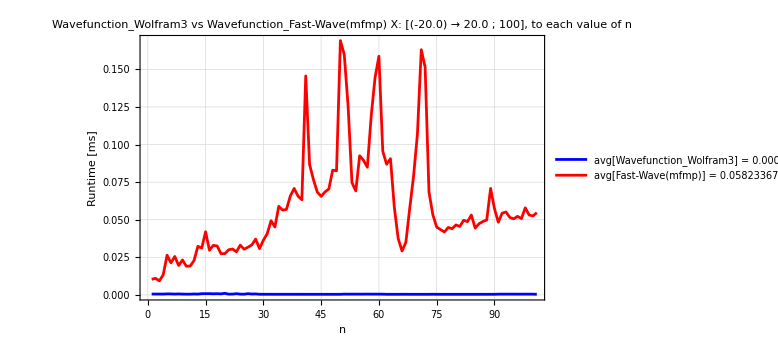

```mathematica
FastWaveMFMDList=Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_numba as wn; import timeit;import numpy as np;N_max = 100;xmax = 20.0;xmin = -20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[(timeit.timeit(lambda : wn.psi_n_multiple_fock_multiple_position(n, X) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframMFMDList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframMFMDList,
RepeatedTiming[WavefunctionMathematica3[i-1,Xvector,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframMFMDList,FastWaveMFMDList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mfmp)",Bold,13],"\n",Style["X: [(-20.0) → 20.0 ; 100], to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram3] = " <>ToString[SetPrecision[Mean[WavefunctionWolframMFMDList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(mfmp)] = "<> ToString[SetPrecision[Mean[FastWaveMFMDList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```